```mathematica
E2[n_,k_, b_]:= E2[n,k,b]=Sum[ E2[n/j,k-1,b],{j,2,n}]-b Sum[ E2[n/(b j),k-1,b],{j,1,n/b}];E2[n_,0,a_]:=1
D1[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D1null[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2null[n/b^j,a],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
```

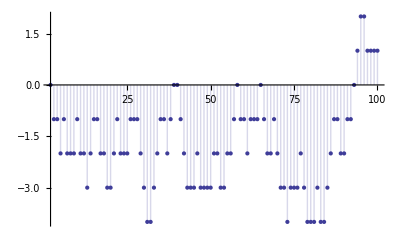

```mathematica
DiscretePlot[ D1[ n, -1, 2], {n,2,100}]
```

```mathematica
D1null[ 100, -1, 6./5]
```

0.-1.2 (E2null[83.3333,0]-E2null[83.3333,1]+E2null[83.3333,2]-E2null[83.3333,3]+E2null[83.3333,4]-E2null[83.3333,5]+E2null[83.3333,6]-E2null[83.3333,7]+E2null[83.3333,8]-E2null[83.3333,9]+E2null[83.3333,10]-E2null[83.3333,11]+E2null[83.3333,12]-E2null[83.3333,13]+E2null[83.3333,14]-E2null[83.3333,15]+E2null[83.3333,16]-E2null[83.3333,17]+E2null[83.3333,18]-E2null[83.3333,19]+E2null[83.3333,20]-E2null[83.3333,21]+E2null[83.3333,22]-E2null[83.3333,23]+E2null[83.3333,24])+1. (E2null[100.,0]-E2null[100.,1]+E2null[100.,2]-E2null[100.,3]+E2null[100.,4]-E2null[100.,5]+E2null[100.,6]-E2null[100.,7]+E2null[100.,8]-E2null[100.,9]+E2null[100.,10]-E2null[100.,11]+E2null[100.,12]-E2null[100.,13]+E2null[100.,14]-E2null[100.,15]+E2null[100.,16]-E2null[100.,17]+E2null[100.,18]-E2null[100.,19]+E2null[100.,20]-E2null[100.,21]+E2null[100.,22]-E2null[100.,23]+E2null[100.,24]-E2null[100.,25])

```mathematica
D1[ 100, -1, 6./5]
```

1.

```mathematica
(-1)^(j+1) (-1)^(k+1)(-1)^(m+1)
```

(-1)^(3+j+k+m)

```mathematica
(-1)^(j+1) (-1)^(k+1)(-1)^(m+1) (-1)^(o+1)
```

(-1)^(4+j+k+m+o)

```mathematica
D1null[ 1000, 1, 7]
```

343 (E2null[1000/343,0]+E2null[1000/343,1])+49 (E2null[1000/49,0]+E2null[1000/49,1])+7 (E2null[1000/7,0]+E2null[1000/7,1])+E2null[1000,0]+E2null[1000,1]

```mathematica
D1null[ 40, 2, 3]
```

108 E2null[40/27,0]+27 (E2null[40/9,0]+2 E2null[40/9,1]+E2null[40/9,2])+6 (E2null[40/3,0]+2 E2null[40/3,1]+E2null[40/3,2])+E2null[40,0]+2 E2null[40,1]+E2null[40,2]

```mathematica
Table[ {n, E2[n,1,2],E2[n,2,2], E2[n,3,2], E2[n,4,2], E2[n,5,2], E2[n,6,2], E2[n,7,2]},{n,900,1000}]//TableForm
```

900 | -1 | 5 | 12 | 56 | 55 | -4 | 118
901 | 0 | 7 | 12 | 56 | 55 | -4 | 118
902 | -1 | 1 | 6 | 56 | 55 | -4 | 118
903 | 0 | 7 | 12 | 56 | 55 | -4 | 118
904 | -1 | 9 | 15 | 52 | 55 | -4 | 118
905 | 0 | 11 | 15 | 52 | 55 | -4 | 118
906 | -1 | 5 | 9 | 52 | 55 | -4 | 118
907 | 0 | 5 | 9 | 52 | 55 | -4 | 118
908 | -1 | 5 | 12 | 52 | 55 | -4 | 118
909 | 0 | 9 | 15 | 52 | 55 | -4 | 118
910 | -1 | -5 | -21 | 28 | 55 | -4 | 118
911 | 0 | -5 | -21 | 28 | 55 | -4 | 118
912 | -1 | 1 | -9 | -4 | 40 | 26 | 118
913 | 0 | 3 | -9 | -4 | 40 | 26 | 118
914 | -1 | 1 | -9 | -4 | 40 | 26 | 118
915 | 0 | 7 | -3 | -4 | 40 | 26 | 118
916 | -1 | 7 | 0 | -4 | 40 | 26 | 118
917 | 0 | 9 | 0 | -4 | 40 | 26 | 118
918 | -1 | -5 | -45 | -56 | 20 | 26 | 118
919 | 0 | -5 | -45 | -56 | 20 | 26 | 118
920 | -1 | -3 | -30 | -60 | 0 | 26 | 118
921 | 0 | -1 | -30 | -60 | 0 | 26 | 118
922 | -1 | -3 | -30 | -60 | 0 | 26 | 118
923 | 0 | -1 | -30 | -60 | 0 | 26 | 118
924 | -1 | -7 | -9 | 24 | 60 | 26 | 118
925 | 0 | -3 | -6 | 24 | 60 | 26 | 118
926 | -1 | -5 | -6 | 24 | 60 | 26 | 118
927 | 0 | -1 | -3 | 24 | 60 | 26 | 118
928 | -1 | 5 | -9 | 16 | 75 | 20 | 118
929 | 0 | 5 | -9 | 16 | 75 | 20 | 118
930 | -1 | -9 | -45 | -8 | 75 | 20 | 118
931 | 0 | -5 | -42 | -8 | 75 | 20 | 118
932 | -1 | -5 | -39 | -8 | 75 | 20 | 118
933 | 0 | -3 | -39 | -8 | 75 | 20 | 118
934 | -1 | -5 | -39 | -8 | 75 | 20 | 118
935 | 0 | 1 | -33 | -8 | 75 | 20 | 118
936 | -1 | 3 | 0 | 12 | 5 | -40 | 118
937 | 0 | 3 | 0 | 12 | 5 | -40 | 118
938 | -1 | -3 | -6 | 12 | 5 | -40 | 118
939 | 0 | -1 | -6 | 12 | 5 | -40 | 118
940 | -1 | -3 | 3 | 24 | 5 | -40 | 118
941 | 0 | -3 | 3 | 24 | 5 | -40 | 118
942 | -1 | -9 | -3 | 24 | 5 | -40 | 118
943 | 0 | -7 | -3 | 24 | 5 | -40 | 118
944 | -1 | -3 | -3 | 16 | 10 | -40 | 118
945 | 0 | 11 | 42 | 68 | 30 | -40 | 118
946 | -1 | 5 | 36 | 68 | 30 | -40 | 118
947 | 0 | 5 | 36 | 68 | 30 | -40 | 118
948 | -1 | 3 | 45 | 80 | 30 | -40 | 118
949 | 0 | 5 | 45 | 80 | 30 | -40 | 118
950 | -1 | -5 | 24 | 68 | 30 | -40 | 118
951 | 0 | -3 | 24 | 68 | 30 | -40 | 118
952 | -1 | -1 | 39 | 64 | 10 | -40 | 118
953 | 0 | -1 | 39 | 64 | 10 | -40 | 118
954 | -1 | -11 | 18 | 52 | 10 | -40 | 118
955 | 0 | -9 | 18 | 52 | 10 | -40 | 118
956 | -1 | -9 | 21 | 52 | 10 | -40 | 118
957 | 0 | -3 | 27 | 52 | 10 | -40 | 118
958 | -1 | -5 | 27 | 52 | 10 | -40 | 118
959 | 0 | -3 | 27 | 52 | 10 | -40 | 118
960 | -1 | 11 | 6 | -8 | 135 | -34 | -1
961 | 0 | 12 | 6 | -8 | 135 | -34 | -1
962 | -1 | 6 | 0 | -8 | 135 | -34 | -1
963 | 0 | 10 | 3 | -8 | 135 | -34 | -1
964 | -1 | 10 | 6 | -8 | 135 | -34 | -1
965 | 0 | 12 | 6 | -8 | 135 | -34 | -1
966 | -1 | -2 | -30 | -32 | 135 | -34 | -1
967 | 0 | -2 | -30 | -32 | 135 | -34 | -1
968 | -1 | 0 | -21 | -36 | 125 | -34 | -1
969 | 0 | 6 | -15 | -36 | 125 | -34 | -1
970 | -1 | 0 | -21 | -36 | 125 | -34 | -1
971 | 0 | 0 | -21 | -36 | 125 | -34 | -1
972 | -1 | -4 | -6 | 44 | 250 | 50 | 20
973 | 0 | -2 | -6 | 44 | 250 | 50 | 20
974 | -1 | -4 | -6 | 44 | 250 | 50 | 20
975 | 0 | 6 | 15 | 56 | 250 | 50 | 20
976 | -1 | 10 | 15 | 48 | 255 | 50 | 20
977 | 0 | 10 | 15 | 48 | 255 | 50 | 20
978 | -1 | 4 | 9 | 48 | 255 | 50 | 20
979 | 0 | 6 | 9 | 48 | 255 | 50 | 20
980 | -1 | 2 | 24 | 96 | 285 | 50 | 20
981 | 0 | 6 | 27 | 96 | 285 | 50 | 20
982 | -1 | 4 | 27 | 96 | 285 | 50 | 20
983 | 0 | 4 | 27 | 96 | 285 | 50 | 20
984 | -1 | 6 | 42 | 92 | 265 | 50 | 20
985 | 0 | 8 | 42 | 92 | 265 | 50 | 20
986 | -1 | 2 | 36 | 92 | 265 | 50 | 20
987 | 0 | 8 | 42 | 92 | 265 | 50 | 20
988 | -1 | 6 | 51 | 104 | 265 | 50 | 20
989 | 0 | 8 | 51 | 104 | 265 | 50 | 20
990 | -1 | -14 | -42 | -28 | 205 | 50 | 20
991 | 0 | -14 | -42 | -28 | 205 | 50 | 20
992 | -1 | -8 | -48 | -36 | 220 | 44 | 20
993 | 0 | -6 | -48 | -36 | 220 | 44 | 20
994 | -1 | -12 | -54 | -36 | 220 | 44 | 20
995 | 0 | -10 | -54 | -36 | 220 | 44 | 20
996 | -1 | -12 | -45 | -24 | 220 | 44 | 20
997 | 0 | -12 | -45 | -24 | 220 | 44 | 20
998 | -1 | -14 | -45 | -24 | 220 | 44 | 20
999 | 0 | -8 | -36 | -20 | 220 | 44 | 20
1000 | -1 | -6 | -19 | -16 | 190 | 24 | 20

```mathematica
b = 7;
Table[ {n,E2[n,1,(b+1)/b]-E2[n-1,1,(b+1)/b], tt[n,b]},{n,1,100}]//TableForm
```

1 | 0 | 0
2 | -1/7 | -1/7
3 | -1/7 | -1/7
4 | -1/7 | -1/7
5 | -1/7 | -1/7
6 | -1/7 | -1/7
7 | -1/7 | -1/7
8 | -1/7 | -1/7
9 | 1 | 1
10 | -1/7 | -1/7
11 | -1/7 | -1/7
12 | -1/7 | -1/7
13 | -1/7 | -1/7
14 | -1/7 | -1/7
15 | -1/7 | -1/7
16 | -1/7 | -1/7
17 | 1 | 1
18 | -1/7 | -1/7
19 | -1/7 | -1/7
20 | -1/7 | -1/7
21 | -1/7 | -1/7
22 | -1/7 | -1/7
23 | -1/7 | -1/7
24 | -1/7 | -1/7
25 | 1 | 1
26 | -1/7 | -1/7
27 | -1/7 | -1/7
28 | -1/7 | -1/7
29 | -1/7 | -1/7
30 | -1/7 | -1/7
31 | -1/7 | -1/7
32 | -1/7 | -1/7
33 | 1 | 1
34 | -1/7 | -1/7
35 | -1/7 | -1/7
36 | -1/7 | -1/7
37 | -1/7 | -1/7
38 | -1/7 | -1/7
39 | -1/7 | -1/7
40 | -1/7 | -1/7
41 | 1 | 1
42 | -1/7 | -1/7
43 | -1/7 | -1/7
44 | -1/7 | -1/7
45 | -1/7 | -1/7
46 | -1/7 | -1/7
47 | -1/7 | -1/7
48 | -1/7 | -1/7
49 | 1 | 1
50 | -1/7 | -1/7
51 | -1/7 | -1/7
52 | -1/7 | -1/7
53 | -1/7 | -1/7
54 | -1/7 | -1/7
55 | -1/7 | -1/7
56 | -1/7 | -1/7
57 | 1 | 1
58 | -1/7 | -1/7
59 | -1/7 | -1/7
60 | -1/7 | -1/7
61 | -1/7 | -1/7
62 | -1/7 | -1/7
63 | -1/7 | -1/7
64 | -1/7 | -1/7
65 | 1 | 1
66 | -1/7 | -1/7
67 | -1/7 | -1/7
68 | -1/7 | -1/7
69 | -1/7 | -1/7
70 | -1/7 | -1/7
71 | -1/7 | -1/7
72 | -1/7 | -1/7
73 | 1 | 1
74 | -1/7 | -1/7
75 | -1/7 | -1/7
76 | -1/7 | -1/7
77 | -1/7 | -1/7
78 | -1/7 | -1/7
79 | -1/7 | -1/7
80 | -1/7 | -1/7
81 | 1 | 1
82 | -1/7 | -1/7
83 | -1/7 | -1/7
84 | -1/7 | -1/7
85 | -1/7 | -1/7
86 | -1/7 | -1/7
87 | -1/7 | -1/7
88 | -1/7 | -1/7
89 | 1 | 1
90 | -1/7 | -1/7
91 | -1/7 | -1/7
92 | -1/7 | -1/7
93 | -1/7 | -1/7
94 | -1/7 | -1/7
95 | -1/7 | -1/7
96 | -1/7 | -1/7
97 | 1 | 1
98 | -1/7 | -1/7
99 | -1/7 | -1/7
100 | -1/7 | -1/7

```mathematica
tt[ n_, b_] := If[ n==1,0,(Mod[n+b-1,b+1]-Mod[n+b,b+1])/b]
```

```mathematica
N[Sum[ tt[n,3]/n,{n,2,200000}]]
```

-0.245355

```mathematica
Et[ n_, k_, b_] := Sum[ tt[ j,b] Et[ n/j, k-1, b],{j,2,n}]; Et[ n_, 0, b_] := 1
```

```mathematica
Et[100,2,7]
```

11/49

```mathematica
E2[ 100,2,8/7]
```

491/49

```mathematica
b = 2;
Table[ {n,E2[n,2,(b+1)/b]-E2[n-1,2,(b+1)/b], Et[ 4 n,2,b]-Et[4( n-1),2,b]},{n,1,100}]//TableForm
```

1 | 0 | 1/4
2 | 0 | -1/2
3 | -3/4 | 1/4
4 | 1 | 1
5 | 3/2 | -1
6 | -4 | -1/2
7 | 9/2 | 9/4
8 | -1 | -2
9 | -5/4 | 1/4
10 | 2 | 1
11 | -3 | -2
12 | -1/2 | 1/2
13 | 0 | 2
14 | 5 | -1
15 | -7 | -1
16 | 15/2 | 5/4
17 | -3 | -3
18 | -2 | 9/2
19 | 0 | 1
20 | 1 | -5
21 | -1/4 | -3/4
22 | 2 | 3
23 | 0 | 1
24 | -6 | -2
25 | 11/2 | 3
26 | -1 | -3
27 | 1/2 | 3/2
28 | 4 | 1
29 | -3 | -3/2
30 | -9/2 | -2
31 | 0 | 9/4
32 | 4 | -3
33 | -7 | 3/2
34 | 11 | 11/2
35 | -1 | -5
36 | -11/4 | 1/4
37 | 0 | 0
38 | -4 | -7/2
39 | -5/2 | 1
40 | 6 | 5
41 | 9/2 | -1
42 | -9 | -1/2
43 | 9/2 | 0
44 | 1 | -3/2
45 | -7/2 | 2
46 | 2 | -1
47 | -3 | -5/2
48 | 2 | 3/2
49 | 1 | 15/4
50 | 4 | -4
51 | -7 | -2
52 | 17/2 | 11/2
53 | -9 | -4
54 | 0 | 2
55 | 2 | 11/2
56 | 3 | -6
57 | -1/4 | -5/4
58 | 2 | 0
59 | 0 | -1/2
60 | -11 | 1/2
61 | 9 | 3/2
62 | -1 | -3
63 | -7/2 | 3
64 | 5 | 7/2
65 | -1 | -3
66 | -9/2 | 1/2
67 | 0 | 1/2
68 | 7 | -2
69 | -7 | -5
70 | 21/2 | 13/2
71 | -3 | -2
72 | -7/2 | 3
73 | 0 | -5/4
74 | -4 | -3
75 | -2 | -1
76 | 4 | 13/2
77 | 2 | -5
78 | -9 | 1
79 | 9 | 5/2
80 | 5 | -11/2
81 | 9/4 | 17/4
82 | 2 | 7/2
83 | -9 | -4
84 | -13/2 | -4
85 | 2 | 4
86 | 2 | -1
87 | -7 | 0
88 | 15 | 1/2
89 | -3 | -3/2
90 | -5 | 3/2
91 | 2 | 13/2
92 | 1 | -5
93 | -5/2 | 1
94 | 2 | 0
95 | 5 | -4
96 | -8 | -3/2
97 | 9/2 | 4
98 | -5 | -11/2
99 | -7/2 | 1
100 | 7 | 15/4

```mathematica
8./3
```

2.66667

```mathematica
4./(3/2)
```

2.66667

```mathematica
N[4/(9/4)]
```

1.77778

```mathematica
5./(3/2)
```

3.33333

```mathematica
N[5/(9/4)]
```

2.22222

```mathematica
6./(3/2)
```

4.

```mathematica
6./(9/4)
```

2.66667

```mathematica
N[5/(3/2)]
```

3.33333

```mathematica
N[4/(3/2)]
```

2.66667

```mathematica
400.^(1/3)
```

7.36806

```mathematica
200.^(1/2)
```

14.1421

```mathematica
133^(1/2.)
```

11.5326

```mathematica
6*7*8
```

336

```mathematica
7*8*9
```

504

```mathematica
(400./6)^(1/2)
```

8.16497

```mathematica
Table[{j+1, Floor[400/6/j]},{j,7,8}]//TableForm
```

8 | 9
9 | 8

```mathematica
E2[33, 1,2]-E2[ 7-1, 1,2]
```

1

```mathematica
D1[ 120, 2, 3/2]
```

602

```mathematica
D2Alt[ n_, a_, b_] := Sum[ (j+1)a^j/b^j ( E2[ n b^j / a^j, 0, a/b] + 2 E2[ n b^j / a^j, 1, a/b] + E2[ n b^j / a^j, 2, a/b] ), { j, 0, Log[n]/( Log[a]-Log[b])}]
D2Alt2[ n_, a_, b_] := Sum[ (j+1)a^j/b^j (1 + 2 E2[ n b^j / a^j, 1, a/b] + E2[ n b^j / a^j, 2, a/b] ), { j, 0, Log[n]/( Log[a]-Log[b])}]
```

```mathematica
D2Alt2[120,4,3]
```

602

```mathematica
MertensAlt[ n_, a_, b_] := Sum[ (-1)^k ( E2[ n, k, a/b] - (a/b)E2[n b / a, k, a/b] ), {k,0, Log[n]/( Log[a]-Log[b])}]
```

```mathematica
DiscretePlot[ MAlt[n,4,3], {n,2,100}]
```

-Graphics-

```mathematica
DiscretePlot[D1[n,-1,4/3], {n,2,100}]
```

-Graphics-

```mathematica
E2i[ n_, a_, b_] := b^-1 If[ n < b+1, 0, (b Floor[n b/b]-a Floor[n b/a])-(b Floor[(b)/b]-a Floor[(b)/a])]
E2j[ n_, a_, b_] := b^-1 If[ n < b+1, 0, (n b -a Floor[n b/a])-(b -a Floor[b/a])]
```

```mathematica
E2[123,1,4/3]
```

-2/3

```mathematica
Grid[Table[ N[E2j[ n, b+1,b]],{n,10,500,10},{b,10,100,10}]]
```

0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.7 | -0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.6 | -0.9 | -0.266667 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | -0.35 | -0.6 | -0.2 | 0. | 0. | 0. | 0. | 0. | 0.
-0.4 | -0.85 | -0.933333 | -0.45 | -0.16 | 0. | 0. | 0. | 0. | 0.
-0.3 | -0.3 | -0.233333 | -0.7 | -0.36 | -0.133333 | 0. | 0. | 0. | 0.
-0.2 | -0.8 | -0.566667 | -0.95 | -0.56 | -0.3 | -0.114286 | 0. | 0. | 0.
-0.1 | -0.25 | -0.9 | -0.175 | -0.76 | -0.466667 | -0.257143 | -0.1 | 0. | 0.
0. | -0.75 | -0.2 | -0.425 | -0.96 | -0.633333 | -0.4 | -0.225 | -0.0888889 | 0.
-1. | -0.2 | -0.533333 | -0.675 | -0.14 | -0.8 | -0.542857 | -0.35 | -0.2 | -0.08
-0.9 | -0.7 | -0.866667 | -0.925 | -0.34 | -0.966667 | -0.685714 | -0.475 | -0.311111 | -0.18
-0.8 | -0.15 | -0.166667 | -0.15 | -0.54 | -0.116667 | -0.828571 | -0.6 | -0.422222 | -0.28
-0.7 | -0.65 | -0.5 | -0.4 | -0.74 | -0.283333 | -0.971429 | -0.725 | -0.533333 | -0.38
-0.6 | -0.1 | -0.833333 | -0.65 | -0.94 | -0.45 | -0.1 | -0.85 | -0.644444 | -0.48
-0.5 | -0.6 | -0.133333 | -0.9 | -0.12 | -0.616667 | -0.242857 | -0.975 | -0.755556 | -0.58
-0.4 | -0.05 | -0.466667 | -0.125 | -0.32 | -0.783333 | -0.385714 | -0.0875 | -0.866667 | -0.68
-0.3 | -0.55 | -0.8 | -0.375 | -0.52 | -0.95 | -0.528571 | -0.2125 | -0.977778 | -0.78
-0.2 | 0. | -0.1 | -0.625 | -0.72 | -0.1 | -0.671429 | -0.3375 | -0.0777778 | -0.88
-0.1 | -0.5 | -0.433333 | -0.875 | -0.92 | -0.266667 | -0.814286 | -0.4625 | -0.188889 | -0.98
0. | -1. | -0.766667 | -0.1 | -0.1 | -0.433333 | -0.957143 | -0.5875 | -0.3 | -0.07
-1. | -0.45 | -0.0666667 | -0.35 | -0.3 | -0.6 | -0.0857143 | -0.7125 | -0.411111 | -0.17
-0.9 | -0.95 | -0.4 | -0.6 | -0.5 | -0.766667 | -0.228571 | -0.8375 | -0.522222 | -0.27
-0.8 | -0.4 | -0.733333 | -0.85 | -0.7 | -0.933333 | -0.371429 | -0.9625 | -0.633333 | -0.37
-0.7 | -0.9 | -0.0333333 | -0.075 | -0.9 | -0.0833333 | -0.514286 | -0.075 | -0.744444 | -0.47
-0.6 | -0.35 | -0.366667 | -0.325 | -0.08 | -0.25 | -0.657143 | -0.2 | -0.855556 | -0.57
-0.5 | -0.85 | -0.7 | -0.575 | -0.28 | -0.416667 | -0.8 | -0.325 | -0.966667 | -0.67
-0.4 | -0.3 | 0. | -0.825 | -0.48 | -0.583333 | -0.942857 | -0.45 | -0.0666667 | -0.77
-0.3 | -0.8 | -0.333333 | -0.05 | -0.68 | -0.75 | -0.0714286 | -0.575 | -0.177778 | -0.87
-0.2 | -0.25 | -0.666667 | -0.3 | -0.88 | -0.916667 | -0.214286 | -0.7 | -0.288889 | -0.97
-0.1 | -0.75 | -1. | -0.55 | -0.06 | -0.0666667 | -0.357143 | -0.825 | -0.4 | -0.06
0. | -0.2 | -0.3 | -0.8 | -0.26 | -0.233333 | -0.5 | -0.95 | -0.511111 | -0.16
-1. | -0.7 | -0.633333 | -0.025 | -0.46 | -0.4 | -0.642857 | -0.0625 | -0.622222 | -0.26
-0.9 | -0.15 | -0.966667 | -0.275 | -0.66 | -0.566667 | -0.785714 | -0.1875 | -0.733333 | -0.36
-0.8 | -0.65 | -0.266667 | -0.525 | -0.86 | -0.733333 | -0.928571 | -0.3125 | -0.844444 | -0.46
-0.7 | -0.1 | -0.6 | -0.775 | -0.04 | -0.9 | -0.0571429 | -0.4375 | -0.955556 | -0.56
-0.6 | -0.6 | -0.933333 | 0. | -0.24 | -0.05 | -0.2 | -0.5625 | -0.0555556 | -0.66
-0.5 | -0.05 | -0.233333 | -0.25 | -0.44 | -0.216667 | -0.342857 | -0.6875 | -0.166667 | -0.76
-0.4 | -0.55 | -0.566667 | -0.5 | -0.64 | -0.383333 | -0.485714 | -0.8125 | -0.277778 | -0.86
-0.3 | 0. | -0.9 | -0.75 | -0.84 | -0.55 | -0.628571 | -0.9375 | -0.388889 | -0.96
-0.2 | -0.5 | -0.2 | -1. | -0.02 | -0.716667 | -0.771429 | -0.05 | -0.5 | -0.05
-0.1 | -1. | -0.533333 | -0.225 | -0.22 | -0.883333 | -0.914286 | -0.175 | -0.611111 | -0.15
0. | -0.45 | -0.866667 | -0.475 | -0.42 | -0.0333333 | -0.0428571 | -0.3 | -0.722222 | -0.25
-1. | -0.95 | -0.166667 | -0.725 | -0.62 | -0.2 | -0.185714 | -0.425 | -0.833333 | -0.35
-0.9 | -0.4 | -0.5 | -0.975 | -0.82 | -0.366667 | -0.328571 | -0.55 | -0.944444 | -0.45
-0.8 | -0.9 | -0.833333 | -0.2 | 0. | -0.533333 | -0.471429 | -0.675 | -0.0444444 | -0.55
-0.7 | -0.35 | -0.133333 | -0.45 | -0.2 | -0.7 | -0.614286 | -0.8 | -0.155556 | -0.65
-0.6 | -0.85 | -0.466667 | -0.7 | -0.4 | -0.866667 | -0.757143 | -0.925 | -0.266667 | -0.75
-0.5 | -0.3 | -0.8 | -0.95 | -0.6 | -0.0166667 | -0.9 | -0.0375 | -0.377778 | -0.85
-0.4 | -0.8 | -0.1 | -0.175 | -0.8 | -0.183333 | -0.0285714 | -0.1625 | -0.488889 | -0.95

```mathematica
Expand[(n (b-1))/b]
```

n-n/b

```mathematica
MertensReference[n_]:=Sum[MoebiusMu[j],{j,1,n}]
alpha[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])-a (Floor[n/a]-Floor[(n-1)/a])
E2[n_,k_,a_,b_]:=E2[n,k,a,b]=(1/b)Sum[If[alpha[j,a,b]==0,0,alpha[j,a,b]E2[(b n)/j,k-1,a,b]],{j,b+1,b n}];E2[n_,0,a_,b_]:=1
MertensAlt[ n_, a_, b_] := Sum[ (-1)^k ( E2[ n, k, a,b] - (a/b)E2[n b / a, k, a,b] ), {k,0, Floor[Log[n]/( Log[a]-Log[b])]}]
Grid[ Table[ {MertensReference[ n ], MertensAlt[ n, b+1, b]},{n,10,100,10},{b,1,5}]]
```

{-1,-1} | {-1,-1} | {-1,-1} | {-1,-1} | {-1,-1}
{-3,-3} | {-3,-3} | {-3,-3} | {-3,-3} | {-3,-3}
{-3,-3} | {-3,-3} | {-3,-3} | {-3,-3} | {-3,-3}
{0,0} | {0,0} | {0,0} | {0,0} | {0,0}
{-3,-3} | {-3,-3} | {-3,-3} | {-3,-3} | {-3,-3}
{-1,-1} | {-1,-1} | {-1,-1} | {-1,-1} | {-1,-1}
{-2,-2} | {-2,-2} | {-2,-2} | {-2,-2} | {-2,-2}
{-4,-4} | {-4,-4} | {-4,-4} | {-4,-4} | {-4,-4}
{-2,-2} | {-2,-2} | {-2,-2} | {-2,-2} | {-2,-2}
{1,1} | {1,1} | {1,1} | {1,1} | {1,1}

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
ReferenceD1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
alpha[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])-a (Floor[n/a]-Floor[(n-1)/a])
E2[n_,k_,a_,b_]:=E2[n,k,a,b]=(1/b)Sum[If[alpha[j,a,b]==0,0,alpha[j,a,b]E2[(b n)/j,k-1,a,b]],{j,b+1,b n}];E2[n_,0,a_,b_]:=1
D1Alt[n_, z_, a_, b_] := Sum[ (-1)^j Binomial[-z,j] Binomial[z,k] a^j/b^j 
 E2[n b^j/a^j,k, a,b], {j,0, Floor[Log[n]/(Log[a]-Log[b])]}, {k,0, Floor[(Log[n]+j Log[b] - j Log[a])/(Log[a]-Log[b])]}]
Grid[ Table[ {ReferenceD1[123, j+1/3 ],D1Alt[ 123, j+1/3, b+1,b]},{j,1,5},{b,1,5}]]
```

{1496045/6561,1496045/6561} | {1496045/6561,1496045/6561} | {1496045/6561,1496045/6561} | {1496045/6561,1496045/6561} | {1496045/6561,1496045/6561}
{6095315/6561,6095315/6561} | {6095315/6561,6095315/6561} | {6095315/6561,6095315/6561} | {6095315/6561,6095315/6561} | {6095315/6561,6095315/6561}
{17459030/6561,17459030/6561} | {17459030/6561,17459030/6561} | {17459030/6561,17459030/6561} | {17459030/6561,17459030/6561} | {17459030/6561,17459030/6561}
{41166875/6561,41166875/6561} | {41166875/6561,41166875/6561} | {41166875/6561,41166875/6561} | {41166875/6561,41166875/6561} | {41166875/6561,41166875/6561}
{85424393/6561,85424393/6561} | {85424393/6561,85424393/6561} | {85424393/6561,85424393/6561} | {85424393/6561,85424393/6561} | {85424393/6561,85424393/6561}

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
ReferenceD1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
alpha[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])-a (Floor[n/a]-Floor[(n-1)/a])
E2[n_,k_,a_,b_]:=E2[n,k,a,b]=(1/b)Sum[If[alpha[j,a,b]==0,0,alpha[j,a,b]E2[(b n)/j,k-1,a,b]],{j,b+1,b n}];E2[n_,0,a_,b_]:=1
DAlt[ n_, a_, b_] := Sum[ (j+1)a^j/b^j ( E2[ n b^j / a^j, 0, a,b] + 2 E2[ n b^j / a^j, 1, a,b] + E2[ n b^j / a^j, 2, a,b] ), { j, 0, Log[n]/( Log[a]-Log[b])}]
Grid[ Table[ {ReferenceD1[n, 2 ],DAlt[ n, b+1,b]},{n,10,100,10},{b,1,7}]]
```

{27,27} | {27,27} | {27,27} | {27,27} | {27,27} | {27,27} | {27,27}
{66,66} | {66,66} | {66,66} | {66,66} | {66,66} | {66,66} | {66,66}
{111,111} | {111,111} | {111,111} | {111,111} | {111,111} | {111,111} | {111,111}
{158,158} | {158,158} | {158,158} | {158,158} | {158,158} | {158,158} | {158,158}
{207,207} | {207,207} | {207,207} | {207,207} | {207,207} | {207,207} | {207,207}
{261,261} | {261,261} | {261,261} | {261,261} | {261,261} | {261,261} | {261,261}
{312,312} | {312,312} | {312,312} | {312,312} | {312,312} | {312,312} | {312,312}
{368,368} | {368,368} | {368,368} | {368,368} | {368,368} | {368,368} | {368,368}
{425,425} | {425,425} | {425,425} | {425,425} | {425,425} | {425,425} | {425,425}
{482,482} | {482,482} | {482,482} | {482,482} | {482,482} | {482,482} | {482,482}

```mathematica
alpha[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])-a (Floor[n/a]-Floor[(n-1)/a])
E1[n_,k_,a_,b_]:=E1[n,k,a,b]=(1/b)Sum[If[alpha[j,a,b]==0,0,alpha[j,a,b]E1[(b n)/j,k-1,a,b]],{j,1,b n}];E1[n_,0,a_,b_]:=1
E2[n_,k_,a_,b_]:=E2[n,k,a,b]=(1/b)Sum[If[alpha[j,a,b]==0,0,alpha[j,a,b]E2[(b n)/j,k-1,a,b]],{j,b+1,b n}];E2[n_,0,a_,b_]:=1
E1Alt[n_,z_,a_,b_]:=Sum[Binomial[z,k] E2[n,k,a,b],{k,0,Floor[Log[n]/(Log[a]-Log[b])]}]
Grid[ Table[ {E1[n,3,b+1,b ],E1Alt[ n, 3,b+1,b]},{n,10,80,10},{b,1,6}]]
```

{-3,-3} | {59/4,59/4} | {-121/27,-121/27} | {-57/16,-57/16} | {-431/125,-431/125} | {-1159/216,-1159/216}
{-6,-6} | {8,8} | {-524/27,-524/27} | {-1097/64,-1097/64} | {-1016/125,-1016/125} | {-1063/108,-1063/108}
{-14,-14} | {-33/2,-33/2} | {196/27,196/27} | {-2731/64,-2731/64} | {-1878/125,-1878/125} | {6619/216,6619/216}
{10,10} | {27/4,27/4} | {-1190/27,-1190/27} | {-451/16,-451/16} | {-1548/125,-1548/125} | {-3053/216,-3053/216}
{-2,-2} | {123/4,123/4} | {820/27,820/27} | {611/64,611/64} | {1434/125,1434/125} | {1181/24,1181/24}
{-2,-2} | {-279/8,-279/8} | {-1118/27,-1118/27} | {-273/4,-273/4} | {-5058/125,-5058/125} | {901/18,901/18}
{-21,-21} | {181/4,181/4} | {-155/9,-155/9} | {-3599/64,-3599/64} | {6851/125,6851/125} | {-6671/72,-6671/72}
{0,0} | {275/8,275/8} | {-220/9,-220/9} | {-757/32,-757/32} | {-3352/125,-3352/125} | {-589/36,-589/36}